```mathematica
iter[f_,z_,0]:=z
iter[f_,z_,n_]:=iter[f,f[z],n-1]
```

```mathematica
f[z_]:=(3z-z^3)/2
```

```mathematica
path[t_]:=2 Sin[2 Pi t]+Sin[2 Pi t]Cos[2 Pi t]ⅈ
Manipulate[ComplexListPlot[z/.RootReduce[Solve[iter[f,z,3]==path[t],z,Complexes]],PlotRange->{{-3,3},{-2,2}}],{t,0,1}]
```

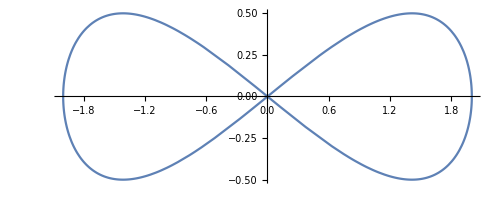

```mathematica
ParametricPlot[{Re[path[t]],Im[path[t]]},{t,0,1}]
```